```mathematica
RK4[f_,t0_,T_,u0_,h_]:=Module[{
n=⌈(T-t0)/h⌉,t,res,i,s,
a=N@{0,1/2,1/2,1},b=N@{0,1/2,1/2,1},p=N@{1/3,1/6,1/6,1/3},k=ConstantArray[0,4]},
t=Table[t0+k*h,{k,0,n}];
res=ConstantArray[0,n+1];
res⟦1⟧=u0;

For[i=1,i≤n,i++,
For[s=1,s≤4,s++,
k⟦s⟧=h*f[t⟦i⟧+a⟦s⟧h,res⟦i⟧+b⟦s⟧ k⟦s-1⟧];
];
res⟦i+1⟧=res⟦i⟧+p.k;
];

{t,res}
]

AB4[f_,t0_,T_,u0_,h_]:=Module[{
n=⌈(T-t0)/h⌉,k,coeffs,func,t,res},
t=Table[t0+i h,{i,0,n}];
res=ConstantArray[0,n+1];
res⟦{1,2,3,4}⟧=RK4[f,t0,t0+3 h,u0,h]⟦2⟧;

func=Table[f[t0+kk h,res⟦kk+1⟧],{kk,0,3}];
coeffs=N@{-3/8,37/24,-59/24,55/24};

For[k=4,k≤n,k++,
res⟦k+1⟧=res⟦k⟧+h func.coeffs;
func=RotateLeft[func,1];
func⟦4⟧=f[t⟦k+1⟧,res⟦k+1⟧];
];

{t,res}
]
```

```mathematica
(* Example *)
f[t_,u_]:=10 u (1-u);
ur[t_]:=0.01/(0.01+0.99 Exp[-10 t]);
T=1;
t0=0;
u0=0.01;
h=0.03;
```

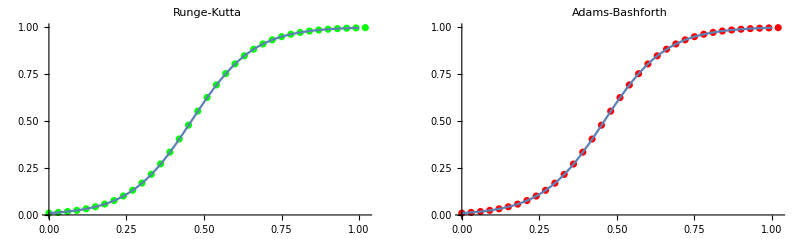

```mathematica
(* Comparison of approximations *)
{xRK,yRK}=RK4[f,t0,T,u0,h];
{xAB,yAB}=AB4[f,t0,T,u0,h];
runge=ListPlot[Thread[{xRK,yRK}],PlotStyle->Green, PlotLabel->"Runge-Kutta"];
adams=ListPlot[Thread[{xAB,yAB}],PlotStyle->Red,PlotLabel->"Adams-Bashforth"];
actual=Plot[ur[t],{t,0,1}];
GraphicsGrid[{{Show[runge,actual],Show[adams,actual]}},Frame->All]
```

```mathematica
Labeled[
First@Timing[For[k2=1,k2≤1000,k2++,ytRK2=RK4[f,t0,T,u0,h];];],
"Time used by 1000 RK4", {Top}
]
```

0.855223Time used by 1000 RK4

```mathematica
Labeled[
First@Timing[For[k3=1,k3≤1000,k3++,ytAB2=AB4[f,t0,T,u0,h];];],
"Time used by 1000 AB4", {Top}
]
```

0.378052Time used by 1000 AB4